```mathematica
p[a_,n_]:=Exp[-a]a^n/n!
```

```mathematica
weekly[n_]:=p[1, n]
```

```mathematica
daily[n_]:=p[1/7, n]
```

```mathematica
monthly[n_]:=p[4, n]
```

```mathematica
N[daily[0]]
```

0.866878

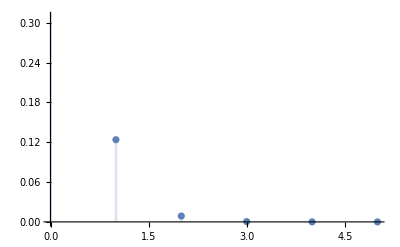

```mathematica
DiscretePlot[daily[n], {n, 0, 5}]
```

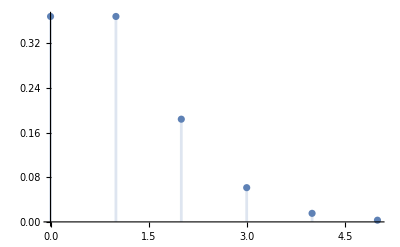

```mathematica
DiscretePlot[weekly[n], {n, 0, 5}]
```

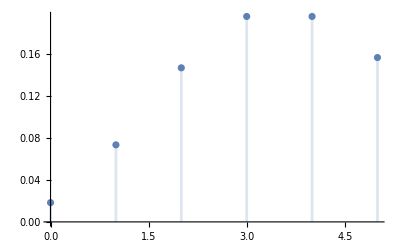

```mathematica
DiscretePlot[monthly[n], {n, 0, 5}]
```